# Zero Temperature Physics of the Full Singlet Model

Isaac R. Wang

This code analyze the zero temperature physics of the naturally light singlet scalar model. The interacting potential is chosen to be of the full form. That means the light scalar is regarded as the angular direction of the scalar in the UV theory.

```mathematica
Quit[];
```

```mathematica
$Assumptions={{μH,λ,μS,A,x1,x2,x3,h,v,w,mS,mh,θ,f,f-S,μHsq,μSsq}∈PositiveReals,π/2<δ<π};
MakeBoxes[μSsq,TraditionalForm]:="μ_S^2";
MakeBoxes[μHsq,TraditionalForm]:="μ_H^2";
MakeBoxes[x1,TraditionalForm]:="x_1";
MakeBoxes[x2,TraditionalForm]:="x_2";
MakeBoxes[x3,TraditionalForm]:="x_3";
MakeBoxes[mh,TraditionalForm]:="m_h";
MakeBoxes[mS,TraditionalForm]:="m_S";
```

## Potential

Define the tree-level potential and take the series.

```mathematica
V0=-(μHsq-A f Cos[δ])(H†.H)+λ (H†.H)^2+μSsq f^2(1-Cos[S/f])-A f( (H†.H)-v^2)Cos[S/f-δ];
dof={H->1/(√2){x1+ⅈ x2,h+ⅈ x3}};
truevev={x1->0,x2->0,x3->0};
physical‵vev={h->√2 v,S->0};
Vtree=V0/.dof//Simplify
Vtree‵nogs=Vtree/.truevev//Simplify
```

1/4 (-2 A f cos(S/f-δ) (h^2+x_1^2+x_2^2+x_3^2-2 v^2)-2 (h^2+x_1^2+x_2^2+x_3^2) (μ_H^2-A f cos(δ))-4 f^2 μ_S^2 (cos(S/f)-1)+λ (h^2+x_1^2+x_2^2+x_3^2)^2)

1/4 (-2 A f (h^2-2 v^2) cos(S/f-δ)-2 h^2 (μ_H^2-A f cos(δ))-4 f^2 μ_S^2 (cos(S/f)-1)+h^4 λ)

```mathematica
Vseries=Series[Vtree‵nogs,{S,0,2}]//Normal
```

```mathematica
1/4 S^2 ((A cos(δ) (h^2-2 v^2))/f+2 Subscript[μ, S]^2)+1/4 (4 A f v^2 cos(δ)+h^4 λ-2 h^2 Subscript[μ, H]^2)-1/2 A S sin(δ) (h^2-2 v^2)
```

```mathematica
Collect[D[Vseries,S],S]
```

1/2 S ((A cos(δ) (h^2-2 v^2))/f+2 μ_S^2)-1/2 A sin(δ) (h^2-2 v^2)

## Tree-level physics

### Mass spectrum

```mathematica
mass‵matrix=D[Vtree,{{x1,x2,x3,h,S},2}]/.truevev//Simplify;
mass‵matrix//MatrixForm
```

(A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2 | 0 | 0 | 0 | 0
0 | A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2 | 0 | 0 | 0
0 | 0 | A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2 | 0 | 0
0 | 0 | 0 | A f cos(δ)-A f cos(S/f-δ)+3 h^2 λ-μ_H^2 | A h sin(S/f-δ)
0 | 0 | 0 | A h sin(S/f-δ) | (A (h^2-2 v^2) cos(S/f-δ))/(2 f)+μ_S^2 cos(S/f))

```mathematica
mStree=Eigenvalues[mass‵matrix[[4;;5,4;;5]]][[1]]//Simplify
mhtree=Eigenvalues[mass‵matrix[[4;;5,4;;5]]][[2]]//Simplify
mgs=mass‵matrix[[1,1]]
```

1/(4 f)(-√((A (2 f^2-h^2+2 v^2) cos(S/f-δ)+2 f (-A f cos(δ)-3 h^2 λ+μ_H^2)-2 f μ_S^2 cos(S/f))^2-4 f (f cos(S/f) (A^2 (h^2-2 v^2)+4 μ_S^2 (3 h^2 λ-μ_H^2))+A (A f (h^2-2 v^2) cos(S/f-2 δ)+A f (h^2+2 v^2) cos((2 S)/f-2 δ)-3 A f h^2+2 A f v^2+2 f^2 μ_S^2 cos(S/f-δ)-2 f^2 μ_S^2 cos((2 S)/f-δ)+2 f^2 μ_S^2 cos(δ+S/f)-2 f^2 μ_S^2 cos(δ)+6 h^4 λ cos(S/f-δ)-2 h^2 μ_H^2 cos(S/f-δ)-12 h^2 λ v^2 cos(S/f-δ)+4 μ_H^2 v^2 cos(S/f-δ))))+2 A f^2 cos(δ)-2 A f^2 cos(S/f-δ)+A h^2 cos(S/f-δ)-2 A v^2 cos(S/f-δ)+6 f h^2 λ+2 f μ_S^2 cos(S/f)-2 f μ_H^2)

1/(4 f)(√((A (2 f^2-h^2+2 v^2) cos(S/f-δ)+2 f (-A f cos(δ)-3 h^2 λ+μ_H^2)-2 f μ_S^2 cos(S/f))^2-4 f (f cos(S/f) (A^2 (h^2-2 v^2)+4 μ_S^2 (3 h^2 λ-μ_H^2))+A (A f (h^2-2 v^2) cos(S/f-2 δ)+A f (h^2+2 v^2) cos((2 S)/f-2 δ)-3 A f h^2+2 A f v^2+2 f^2 μ_S^2 cos(S/f-δ)-2 f^2 μ_S^2 cos((2 S)/f-δ)+2 f^2 μ_S^2 cos(δ+S/f)-2 f^2 μ_S^2 cos(δ)+6 h^4 λ cos(S/f-δ)-2 h^2 μ_H^2 cos(S/f-δ)-12 h^2 λ v^2 cos(S/f-δ)+4 μ_H^2 v^2 cos(S/f-δ))))+2 A f^2 cos(δ)-2 A f^2 cos(S/f-δ)+A h^2 cos(S/f-δ)-2 A v^2 cos(S/f-δ)+6 f h^2 λ+2 f μ_S^2 cos(S/f)-2 f μ_H^2)

A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2

```mathematica
physical‵matrix=mass‵matrix[[4;;5,4;;5]]/.physical‵vev//Simplify;
physical‵matrix//MatrixForm
```

(6 λ v^2-μ_H^2 | -√2 A v sin(δ)
-√2 A v sin(δ) | μ_S^2)

The [1,1] and [2,2] term should be positive so that the extremum is minimum, not maximum.

### Vev

We fix the vev of S to be 0. This can be ensured simply by field redefinition.

```mathematica
D[Vtree‵nogs,{{S,h}}]//Simplify
```

{1/2 A (h^2-2 v^2) sin(S/f-δ)+f μ_S^2 sin(S/f),h (A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2)}

```mathematica
D[Vtree‵nogs,{{S,h}}]/.{h->√2 v}//Simplify
```

{f μ_S^2 sin(S/f),√2 v (A f cos(δ)-A f cos(S/f-δ)-μ_H^2+2 λ v^2)}

```mathematica
der=D[Vtree‵nogs,{{S,h}}]/.{h->√2 v,S->0}//Simplify
```

{0,√2 v (2 λ v^2-μ_H^2)}

```mathematica
D[Vtree‵nogs,{{S,h}}]/.{h->√2 v,S->f π}//Simplify
```

{0,√2 v (2 A f cos(δ)-μ_H^2+2 λ v^2)}

```mathematica
(*cosβ=Cos[β]/.Solve[der[[1]]==0,Cos[β]][[1]]//Normal*)
```

```mathematica
μHsol=Solve[der[[2]]==0,μHsq][[1]]//Normal//Simplify
```

{μ_H^2→2 λ v^2}

For the path of minimizing the S, we have

```mathematica
dVdS=D[Vtree‵nogs,S]//TrigExpand
```

1/2 A h^2 cos(δ) sin(S/f)-1/2 A h^2 sin(δ) cos(S/f)-A v^2 cos(δ) sin(S/f)+A v^2 sin(δ) cos(S/f)+f μ_S^2 sin(S/f)

```mathematica
Collect[dVdS,{Cos[S/f],Sin[S/f],A}]
```

sin(S/f) (A (1/2 h^2 cos(δ)-v^2 cos(δ))+f μ_S^2)+A cos(S/f) (v^2 sin(δ)-1/2 h^2 sin(δ))

Make it of the form K sin[S/f+ϕ]. K is positive.

```mathematica
a=Coefficient[dVdS,Sin[S/f]]
b=Coefficient[dVdS,Cos[S/f]]
K=√(a^2+b^2)//Simplify
ϕ=ArcTan[b/a]//Simplify
Spath=-f ϕ
```

1/2 A h^2 cos(δ)-A v^2 cos(δ)+f μ_S^2

A v^2 sin(δ)-1/2 A h^2 sin(δ)

√((1/2 A cos(δ) (h^2-2 v^2)+f μ_S^2)^2+(A v^2 sin(δ)-1/2 A h^2 sin(δ))^2)

-tan^-1((A sin(δ) (h^2-2 v^2))/(A cos(δ) (h^2-2 v^2)+2 f μ_S^2))

f tan^-1((A sin(δ) (h^2-2 v^2))/(A cos(δ) (h^2-2 v^2)+2 f μ_S^2))

### Parametrization

Note that this guarantees the [1,1] term of the mass matrix to be 4 λv^2 which is positive-definite.

```mathematica
matrix‵vev=physical‵matrix/.μHsol//Simplify;
matrix‵vev//MatrixForm
```

(4 λ v^2 | -√2 A v sin(δ)
-√2 A v sin(δ) | μ_S^2)

```mathematica
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
P//MatrixForm
Diag‵mass={{mh^2,0},{0,mS^2}};
Diag‵mass//MatrixForm
rotated=P.Diag‵mass.Inverse[P]//Simplify;
rotated//MatrixForm
```

(cos(θ) | sin(θ)
-sin(θ) | cos(θ))

(m_h^2 | 0
0 | m_S^2)

(1/2 (cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2) | -(sin(θ) cos(θ) (m_h^2-m_S^2))
-(sin(θ) cos(θ) (m_h^2-m_S^2)) | 1/2 (cos(2 θ) (m_S^2-m_h^2)+m_h^2+m_S^2))

```mathematica
sol‵tree=Solve[{rotated[[1,1]]==matrix‵vev[[1,1]],rotated[[1,2]]==matrix‵vev[[1,2]],rotated[[2,2]]==matrix‵vev[[2,2]]},{A,μSsq,λ}][[1]]//Normal//Simplify
```

{A→(csc(δ) sin(θ) cos(θ) (m_h^2-m_S^2))/(√2 v),μ_S^2→1/2 (cos(2 θ) (m_S^2-m_h^2)+m_h^2+m_S^2),λ→(cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2)/(8 v^2)}

```mathematica
μHsol/.sol‵tree
```

{μ_H^2→1/4 (cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2)}

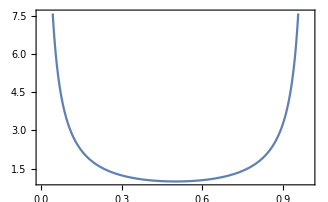

```mathematica
Plot[Csc[δ π],{δ,0,1}]
```

### Benchmark point

```mathematica
num={v->174.,mh->125.13,mS->5,θ->ArcSin[0.1],δ->(4π)/5};
numsol={A,μSsq,λ}/.sol‵tree/.num
```

{10.7538,181.325,0.127999}

```mathematica
μHsq/.μHsol/.sol‵tree/.num
```

7750.6

```mathematica
physical‵matrix‵num=matrix‵vev/.sol‵tree/.num
Eigenvalues[physical‵matrix‵num]^(1/2)
```

(15501.2 | -1555.42
-1555.42 | 181.325)

{125.13,5.}

```mathematica
Vtree‵num=(Vtree‵nogs//TrigExpand)/.μHsol/.sol‵tree/.num/.{f->3681};
```

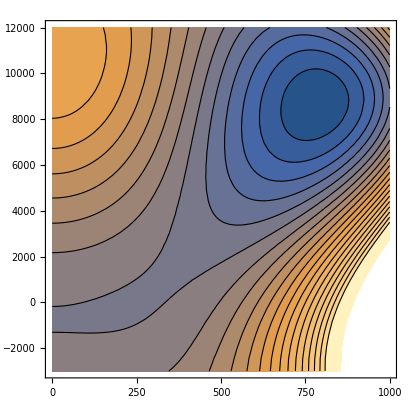

```mathematica
ContourPlot[Vtree‵num,{h,0,1000},{S,-3000,12000},Contours->20]
```

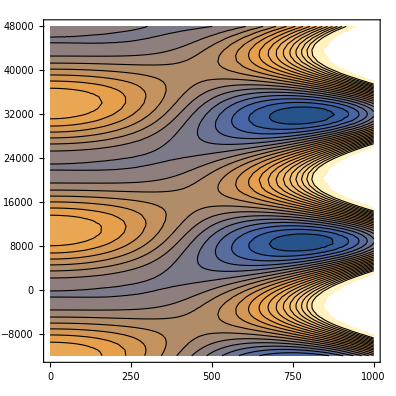

```mathematica
ContourPlot[Vtree‵num,{h,0,1000},{S,-3000*4,12000*4},Contours->20]
```

```mathematica
Slist=Table[{hscan,S/.Minimize[{Vtree‵num/.{h->hscan},-2000<S<12000},S][[2]]},{hscan,0,1000,2}];
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
Spathnum[h_]=Interpolation[Slist][h]
```

InterpolatingFunction[…](h)

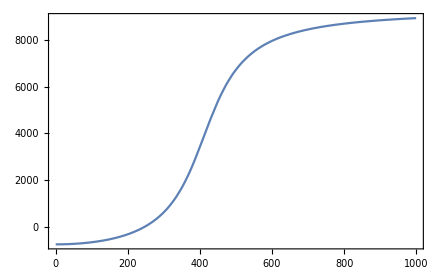

```mathematica
Plot[Spathnum[h],{h,0,1000}]
```

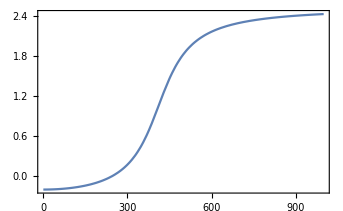

```mathematica
Plot[Spathnum[h]/3681,{h,0,1000}]
```

```mathematica
v1=h/.Minimize[{Vtree‵num/.{S->Spathnum[h]},h>300},h][[2]]
```

784.926

```mathematica
S1=Spathnum[v1]
```

8666.22

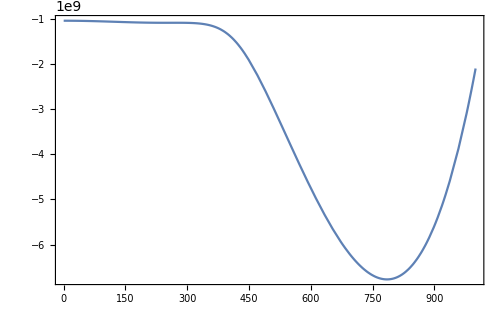

```mathematica
Plot[Vtree‵num/.{S->Spathnum[h]},{h,0,1000}]
```

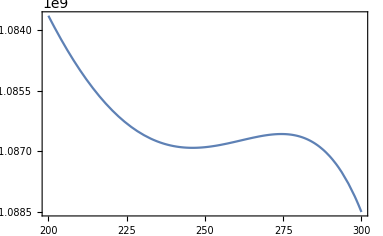

```mathematica
Plot[Vtree‵num/.{S->Spathnum[h]},{h,200,300}]
```

### Rescale

```mathematica
Vre=Vtree‵num/.{h->v1/(√2 174.)h}
```

3.31286 h^4-118371. h^2 sin(S/3681)+162924. h^2 cos(S/3681)-202355. h^2+7.04444×10^8 sin(S/3681)-3.4265×10^9 cos(S/3681)+2.45691×10^9

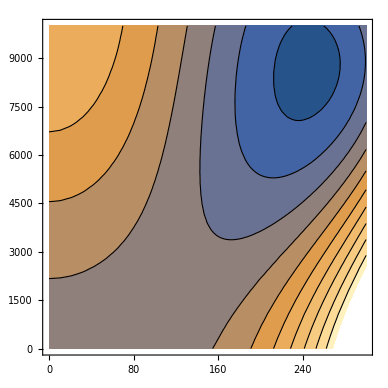

```mathematica
ContourPlot[Vre,{h,0,300},{S,0,10000}]
```

```mathematica
D[Vre,{{h,S},2}]/.{h->√2 174.,S->S1}
```

(1.6048×10^6 | -4262.06
-4262.06 | 673.307)

### New

```mathematica
Vtreenew=Vtree‵nogs/.{v->v1/(√2),μHsq->v1^2 λ}
```

1/4 (-2 A f (h^2-v1^2) cos(S/f-δ)-2 h^2 (λ v1^2-A f cos(δ))-4 f^2 μ_S^2 (cos(S/f)-1)+h^4 λ)

```mathematica
massmatrix=D[Vtreenew,{{h,S},2}]//Simplify
```

(A f cos(δ)-A f cos(S/f-δ)+3 h^2 λ-λ v1^2 | A h sin(S/f-δ)
A h sin(S/f-δ) | (A (h^2-v1^2) cos(S/f-δ))/(2 f)+μ_S^2 cos(S/f))

```mathematica
dvev=D[Vtreenew,{{h,S}}]//Simplify
```

{h (A f cos(δ)-A f cos(S/f-δ)+λ (h^2-v1^2)),1/2 A (h^2-v1^2) sin(S/f-δ)+f μ_S^2 sin(S/f)}

```mathematica
Asol=Solve[massmatrix[[1,2]]==rotated[[1,2]],A][[1]]//Normal
```

{A→(csc(S/f-δ) (m_S^2 sin(2 θ)-m_h^2 sin(2 θ)))/(2 h)}

```mathematica
obs={h->v,S->β f};
num={f->5000,mS->5,θ->ArcSin[0.1],β->3π/4,mh->125.13,v->246.};
```

```mathematica
(dvev[[2]]/.Asol/.obs//Simplify)
```

f μ_S^2 sin(β)-(sin(2 θ) (m_h^2-m_S^2) (v^2-v1^2))/(4 v)

```mathematica
μSsqsol=Solve[(dvev[[2]]/.Asol/.obs//Simplify)==0,μSsq,PositiveReals][[1]]//Normal//Simplify
```

{μ_S^2→(csc(β) sin(2 θ) (m_h^2-m_S^2) (v^2-v1^2))/(4 f v)}

```mathematica
eqns={(massmatrix[[1,1]]/.Asol/.μSsqsol/.obs)==rotated[[1,1]],(massmatrix[[2,2]]/.Asol/.μSsqsol/.obs)==rotated[[2,2]],(dvev[[1]]/.Asol/.μSsqsol/.obs)==0}//Simplify
```

{(f sin(2 θ) (m_h^2-m_S^2) cot(β-δ)-f cos(δ) sin(2 θ) (m_h^2-m_S^2) csc(β-δ)+6 λ v^3-2 λ v v1^2)/(2 v)==1/2 (cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2),2 f v cos(2 θ) (m_h^2-m_S^2)==2 f v (m_h^2+m_S^2)+csc(β) sin(δ) sin(2 θ) (m_h^2-m_S^2) (v^2-v1^2) csc(β-δ),f sin(2 θ) (m_h^2-m_S^2) cot(β-δ)+2 λ v (v^2-v1^2)==f cos(δ) sin(2 θ) (m_h^2-m_S^2) csc(β-δ)}

```mathematica
eqns/.num//Simplify
```

{31614.1 cot(δ+π/4)+31614.1 cos(δ) csc(δ+π/4)+1. λ v1^2+15501.2==181548. λ,(1. v1^2-60516.) sin(δ) csc(δ+π/4)==202783.,λ (2.97739×10^7-492. v1^2)-1.55542×10^7 cot(δ+π/4)==1.55542×10^7 cos(δ) csc(δ+π/4)}

```mathematica
NSolve[eqns/.num,{λ,δ,v1}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{λ→0.128075,δ→-1.68534,v1→-469.47},{λ→0.128075,δ→1.45625,v1→-469.47},{λ→0.128075,δ→-0.158132,v1→0.-833.844 ⅈ},{λ→0.128075,δ→2.98346,v1→0.-833.844 ⅈ},{λ→0.128075,δ→-0.158132,v1→0.+833.844 ⅈ},{λ→0.128075,δ→2.98346,v1→0.+833.844 ⅈ},{λ→0.128075,δ→-1.68534,v1→469.47},{λ→0.128075,δ→1.45625,v1→469.47}}